Universidad de Jaén. EPS Jaén.
Departamento de Matemáticas. Grado en Ingeniería Informática
Análisis y Métodos Numéricos.

## Problemas. Tema 5. Derivación de funciones reales de variable real

## 1.- Justifica que la ecuación x^2=xsenx+cosx tiene una única solución en el intervalo [1,π/2]

Solución :
Consideremos la función f(x)=x^2-xsenx-cosx que es una función continua y derivable. Además, tenemos que
	f(1)=1-1*sen1-cos1<0
	f(π/2)=(π/2)^2-π/2*sen(π/2)-cos(π/2)>0
la función cambia de signo en el intervalo [1,π/2], por tanto, por el Teorema de Bolzano sabemos que la función tiene, al menos, un cero en el intervalo [1,π/2]. Veamos que esa raíz es única, calculemos f’[x]
	f'(x)=2x-senx-xcosx+senx=x(2-cosx)
Busquemos los puntos que anulan la derivada
	f'(x)=0⇔x(2-cosx)=0⇔{x=0
2-cosx=0⟹cosx=2⟹No existe solución real
Tenemos que la derivada solo se anula en x=0 que no es un punto del intervalo  [1,π/2], por lo que por el Teorema de conservación del signo la derivada tendrá el mismo signo en todo el dominio, así
	f'(π/4)=π/4(2-cos(π/4))>0
Tenemos, f(x) una función continua y derivable cuya derivada es positiva, es decir, la función es creciente en todo su dominio. Entonces, se tiene que la función tiene un único cero en el intervalo [1,π/2]. (Si la función solo crece no hay posibilidad de que corte dos veces al eje en el intervalo)

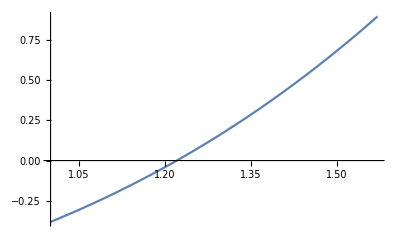

```mathematica
Plot[x^2-x*Sin[x]-Cos[x],{x,1,Pi/2}]
```

## 2.- Demostrar que la recta y=−x es tangente a la curva dada por la ecuación: y=x^3−6x^2+8x. Hallar el punto de tangencia.

Solución : 
La recta tangente a la curva f(x) en el punto x_0 viene dada por la ecuación r(x)=f'(x_0)(x-x_0)+f(x_0). Sabemos que la recta y=-x es tangente a la curva en el punto x_0, por lo que la pendiente de la curva será la derivada en el punto, esto es f'(x_0)=-1.
f(x)=x^3-6 x^2+8x⟹f'(x)=3 x^2-12x+8
f'(x_0)=-1⟺3 x_0^2-12 x_0+8=-1⟺3 x_0^2-12 x_0+9=0⟺(x-1)(x-3)=0⟺x=1
x=3

Los dos candidatos son x=1 y x=3, calculemos las dos rectas y comprobemos cual de ellos es.
	x=1 ⟹r(x)=f'(1)(x-1)+f(1)=-1(x-1)+3=4-x
	x=3⟹r(x)=f'(1)(x-3)+f(3)=-1(x-3)-3=-x

La recta y=-x es tangente a la curva f(x)=x^3-6 x^2+8x en el punto x=3

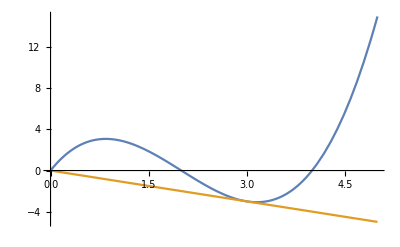

```mathematica
Plot[{x^3-6x^2+8x,-x},{x,0,5}]
```

## 3.- Hallar los puntos de la gráfica de f(x) = 12x - x^3 en los que la recta tangente sea horizontal.

Solución : 
La recta tangente a una curva f(x) en un punto es una recta horizontal si su pendiente, su derivada, es cero. 
f(x)=12x-x^3⟹f'(x)=12-3x^2⟹f'(x)=0⟺12-3 x^2=0⟺x=±2
La recta tangente a la curva f(x) es horizontal en dos puntos, en x=-2 y en x=2. Estos puntos son puntos críticos de la función

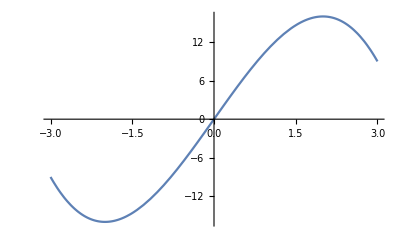

```mathematica
Plot[12x-x^3,{x,-3,3}]
```

## 4.- Calcular la derivada implícita de la función x^3y^4 - e^-y + sen(x) - 3y= 0.

Solución :
x^3 y^4-e^-y+sen(x)-3y=0
3 x^2 y^4+4 x^3 y^3 y'+y' e^-y+cos(x)-3y'=0
(4 x^3 y^3+e^-y-3)y'=-3 x^2 y^4-cos(x)
y'=(-3 x^2 y^4-cos(x))/(4 x^3 y^3+e^-y-3)

Con Mathematica

```mathematica
Solve[D[x^3*(y[x])^4-Exp[-y[x]]+Sin[x]-3y[x]==0,x],y'[x]]//Simplify
```

{{y'[x]→-(ⅇ^y[x] (Cos[x]+3 x^2 y[x]^4))/(1-3 ⅇ^y[x]+4 ⅇ^y[x] x^3 y[x]^3)}}

## 5.- Halla los extremos relativos de la función f(x)=x^3-|x|

Solución :
Toda función con valor absoluto es una función definida a trozos, así la función dada la podemos ver como
f(x)=x^3-|x|={x^3-(-x)
x^3-(x)si x<0
si x>=0={x^3+x
x^3-xsi x<0
si x>=0

Los candidatos a extremos relativos son los puntos donde se anula la derivada, para poder derivar la función tenemos que comprobar si es continua en todo R. Que se puede ver claramente que sí, pues los límites laterales en x=0 coinciden y lo hacen también con el valor de la función en el punto. Calculamos la derivada e igualamos a cero
f'(x)={3 x^2+1
3 x^2-1si x<0
si x>=0⟹f'(x)=0⟺{3 x^2+1=0 No tiene solución real
3 x^2-1=0⟺x=±1/(√3) pero x=-1/(√3)∉[0,∞)
El candidato a extremo relativo es  x=1/(√3), estudiamos el signo de la segunda derivada en el punto
f''(x)={6x
6xsi x<0
si x>=0
	f''(1/(√3))=6*1/(√3)=2 √3>0 ⟹ En x=-1/(√3) hay un mínimo relativo

Con Mathematica

```mathematica
f[x_]:=Piecewise[{{x^3+x,x<0},{x^3-x,x>=0}}]
```

```mathematica
Solve[f'[x]==0,x]
```

{{x→1/(√3)}}

```mathematica
f''[1/(√3)]
```

2 √3

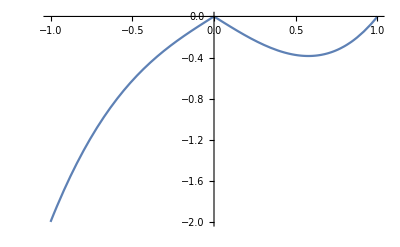

```mathematica
Plot[f[x],{x,-1,1}]
```

## 6.- Calcula los siguientes límites a) Lim_(x->0)(x(e^x+1)-2(e^x-1))/x^3 b) Lim_(x->0)(x^2 sen(1/x))/(sen(x))

Solución :
 a) Lim_(x->0)(x(e^x+1)-2(e^x-1))/x^3=[0/0,L'Hopital]=Lim_(x->0)(1+e^x(x-1))/(3 x^2)=[0/0,L'Hopital]=Lim_(x->0)xe^x/(6x)=Lim_(x->0)e^x/6=1/6

## 7.- Estudia la monotonía, los extremos relativos, puntos de inflexión y la concavidad de la función f(x)=x^3/(x^2-1)

Solución:
La función f(x) es una función continua en su dominio por ser un cociente de polinomios (también es derivable por la misma razón). Comencemos estudiando su dominio, al ser una racional, el dominio es todo R menos los puntos que anulan el denominador
x^2-1=0⟺x=±1
Luego, Dom(f(x))=R-{-1,1}

Los máximos y mínimos relativos se encuentran en los puntos donde se anula la primera derivada:
	Busquemos sus puntos críticos
			f'(x)=(3x^2(x^2-1)-2x*x^3)/((x^2-1)^2)=(x^4-3 x^2)/((x^2-1)^2)=(x^2(x^2-3))/((x^2-1)^2)
			f'(x)=0⟺(x^2(x^2-3))/((x^2-1)^2)=0⟺x^2(x^2-3)=0⟺x^2=0⟺x=0
x^2-3=0⟺x=±√3

	Se han obtenido tres candidatos a extremos relativos x=0,x=-√3 y x=√3 . Estudiemos cada punto aplicando el criterio de la primera derivada. Aprovechamos los cálculos para estudiar la monotonía, para el estudio de la monotonía se tienen en cuenta los puntos que no son del dominio y los puntos críticos, esto hace que el conjunto R se divida en intervalos y por el teorema de conservación del signo podemos estudiar el signo de la derivada en cada uno de estos intervalos
	(-∞,-√3)⟶f''(-10)=((-10)^2((-10)^2-3))/(((-10)^2-1)^2)>0
	(-√3,-1)⟶f''(-1.5)=((-1.5)^2((-1.5)^2-3))/(((-1.5)^2-1)^2)<0
	(-1,0)⟶f''(-0.5)=((-0.5)^2((-0.5)^2-3))/(((-0.5)^2-1)^2)<0
	(1,√3)⟶f'(1.5)=((1.5)^2((1.5)^2-3))/(((1.5)^2-1)^2)<0
	(√3,∞)⟶f'(10)=(10^2(10^2-3))/((10^2-1)^2)>0
La función crece (-∞,-√3)∪(√3,∞)y decrece en (-√3,√3). Además, sabemos que hay un máximo en x=-√3 y un mínimo en x=√3.
Estudiemos la concavidad, para ello busquemos los puntos donde se anula la segunda derivada
	f''(x)=(2x(2 x^2-3)(x^2-1)^2-2(x^2-1)*2x(x^2(x^2-3)))/((x^2-1)^4)=(2x(2 x^2-3)(x^2-1)-2*2x(x^2(x^2-3)))/((x^2-1)^3)=(2x(x^2+3))/((x^2-1)^3)
			f''(x)=0⟺(2x(x^2+3))/((x^2-1)^3)=0⟺2x(x^2+3)=0⟺2x=0⟺x=0
x^2+3=0⟺No existe solución real
El único candidato a punto de inflexión es x=0. Estudiemos la concavidad aplicando la regla de la segunda derivada. Para ello debemos de tener en cuenta los puntos que no son del dominio y los puntos donde se anula la primera y segunda derivada, todos estos puntos me parten el conjunto R en intervalos, estudiamos el signo de la segunda derivada en cada uno de ellos
	(-∞,-√3)⟶f'(-10)<0
	(-√3,-1)⟶f'(-1.5)<0
	(-1,0)⟶f'(-0.5)>0
	(0,1)⟶f''(0.5)<0
	(1,√3)⟶f''(1.5)>0
	(√3,∞)⟶f''(10)>0
Por tanto, tenemos tres puntos de inflexión los puntos x=-1,x=0 y x=1. La función es convexa (∪) en (-1,0)∪(1,∞)y la función es cóncava (∩) en (-∞,-1)∪(0,1)

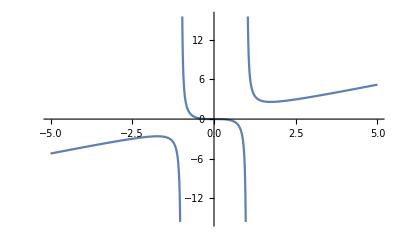

```mathematica
f[x_]:=x^3/(x^2-1)
Plot[f[x],{x,-5,5}]
```

## 8.- Dada la función f(x) = 3x^4-16x^3+18x^2 Calcular, si existen, los valores extremos absolutos de la función f(x) en el intervalo [-1,4]

Solución:
La función f(x) es una función continua por ser un polinomio (también es derivable por la misma razón). Al ser una función continua en un intervalo cerrado y acotado, el [-1, 4], tiene máximo y mínimo absolutos.

Los candidatos a máximos y mínimos absolutos se encuentran estudiando tres tipos de puntos:
	a) Los extremos del intervalo. En este caso, x=-1 y x=4.

	b) Los puntos del interior del intervalo con derivada cero.
		f'(x)=12 x^3-48 x^2+36x=12x(x^2-4x+3)
		f'(x)=0⟺12x(x-1)(x-3)=0⟺{12x=0⟹x=0
(x-1)(x-3)=0⟹x=1
x=3
	La derivada se anula dentro del intervalo en tres puntos  x=0, x=1 y x=3

	c) Los puntos donde no existe derivada. En este caso, la derivada existe en todos los puntos.

Basta ahora evaluar la función en los puntos que hemos encontrado:
f(-1)=3(-1)^4-16(-1)^3+18(-1)^2=3+16+18=37
f(0)=3*0^4-16*0^3+18*0^2=0
f(1)=3*1^4-16*1^3+18*1^2=3-16+18=5
f(3)=3*3^4-16*3^3+18*3^2=3+16+18=243-432+162=-27
f(4)=3*4^4-16*4^3+18*4^2=768-1024+288=32

El valor máximo de la función es 37, que se alcanza en el punto x=-1. El valor mínimo de la función es -27 que se alcanza en el punto x=3.
Si dibujamos la gráfica con el Mathematica vemos lo que ocurre con la función.

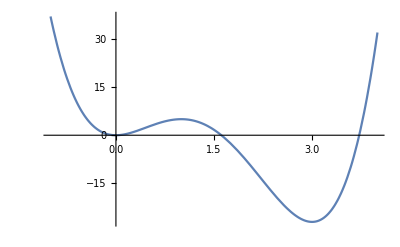

```mathematica
Plot[3x^4-16x^3+18x^2,{x,-1,4}]
```

Con Mathematica:

```mathematica
f[x_]:=3x^4-16x^3+18x^2
```

```mathematica
f'[x]//Factor
```

12 (-3+x) (-1+x) x

```mathematica
Solve[f'[x]==0,x]
```

{{x→0},{x→1},{x→3}}

```mathematica
{f''[0],f''[1],f''[3]}
```

{36,-24,72}

La función tiene un máximo relativo en x=1 y dos mínimos relativos en x=0 y x=3.

```mathematica
{f[-1],f[0],f[1],f[3],f[4]}
```

{37,0,5,-27,32}

La función tiene un máximo absoluto en x=-1 que vale 37 y un mínimo absoluto en x=3 que vale -27

```mathematica
Plot[f[x],{x,-1,4}]
```

-Graphics-

## 9.- Una pista de atletismo tiene forma de rectángulo con dos semicírculos en los extremos, y tiene un perímetro de 50m. Encontrar las dimensiones del terreno para que tenga el área máxima.

## 10.- Estudiar la monotonía, extremos relativos y extremos absolutos de la función f(x) =1/3 x^3-x^2-3x + 4 en los siguientes dominios: ( a ) ℝ ( b ) [0,1] ( c ) [-2,4] ( d ) [0,4]

Solución :
La función f(x)=x^3/3-x^2-3x+4 es una función continua (por ser un polinomio) y el dominio es todo R. También es derivable por la misma razón.

Busquemos sus puntos críticos
f'(x)=x^2-2x-3
f'(x)=0⟺x^2-2x-3=0⟺(x+1)(x-3)=0⟺x=-1
x=3

Estudiemos los extremos relativos
f''(x)=2x-2
f''(-1)=2(-1)-2=-4
f''(3)=2*3-2=4

Estudiemos los intervalos de monotonía
(-∞,-1) ⟶f'(-10)=(-10)^2-2(-10)-3>0
(-1,3) ⟶f'(0)=0^2-2*0-3<0
(3,∞) ⟶f'(10)=10^2-2*10-3>0

( a ) ℝ
	La función tiene en x=-1 un máximo relativo y en x=3 un mínimo relativo. No tiene extremos absolutos porque ℝ no es un intervalo cerrado y acotado.
	La función es creciente en (-∞,-1)∪(3,∞) y decreciente en (-1,3)

( b ) [0,1]
	El intervalo [0,1] es un intervalo cerrado acotado y la función f(x) es continua y derivable en el intervalo,entonces el teorema de Weierstrass asegura 	que existe máximo y mínimo absolutos. Para encontrarlos debemos estudiar los extremos del intervalo (x=0 y x=1), los puntos con derivada 0 del 	interior del intervalo (ninguno de los puntos que anula la derivada pertenecen al intervalo [0,1]), y los puntos donde no exista derivada de la función 	(la derivada existe para todo punto de R).

	Evaluamos los puntos en los candidatos
		f(0)=0^3/3-0^2-3*0+4=4
		f(1)=1^3/3-1^2-3*1+4=1/3-1-3+4=1/3

	La función tiene un máximo absoluto en x=0 y vale 4 y un mínimo absoluto en x=1 y vale 1/3.
	La función es decreciente en todo el intervalo (0,1)

( c ) [-2,4]
	El intervalo [-2,4] es un intervalo cerrado acotado y la función f(x) es continua y derivable en el intervalo,entonces el teorema de Weierstrass asegura 	que existe máximo y mínimo absolutos. Para encontrarlos debemos estudiar los extremos del intervalo (x=-2 y x=4), los puntos con derivada 0 del 	interior del intervalo (x=-1 y x=3), y los puntos donde no exista derivada de la función (la derivada existe para todo punto de R)

	Evaluamos los puntos en los candidatos
		f(-2)=(-2)^3/3-(-2)^2-3*(-2)+4=-8/3-4+6+4=10/3
		f(-1)=(-1)^3/3-(-1)^2-3*(-1)+4=-1/3-1+3+4=-8/3
		f(3)=3^3/3-3^2-3*3+4=9-9-9+4=-5
		f(4)=4^3/3-4^2-3*4+4=64/3-16-12+4=-8/3

	La función tiene un máximo absoluto en x=-1 y vale -8/3 y un mínimo absoluto en x=3 y vale -5.
	La función es creciente en (-2,-1)∪(3,4) y decreciente en (-1,3)


( d ) [0,4]
	El intervalo [0,4] es un intervalo cerrado acotado y la función f(x) es continua y derivable en el intervalo,entonces el teorema de Weierstrass asegura 	que existe máximo y mínimo absolutos. Para encontrarlos debemos estudiar los extremos del intervalo (x=0 y x=4), los puntos con derivada 0 del 	interior del intervalo (x=3), y los puntos donde no exista derivada de la función (la derivada existe para todo punto de R)

	Evaluamos los puntos en los candidatos
		f(0)=0^3/3-0^2-3*0+4=4
		f(3)=3^3/3-3^2-3*3+4=9-9-9+4=-5
		f(4)=4^3/3-4^2-3*4+4=64/3-16-12+4=-8/3

	La función tiene un máximo absoluto en x=0 y vale 4 y un mínimo absoluto en x=3 y vale -5
	La función es creciente en (3,4) y decreciente en (0,3)

## 11.- Obtén la recta normal a la función f (x) = x^2 + 1/2 en el punto x = 0.5

Solución :
La ecuación de la recta normal a la curva en el punto x_0 viene dada por n(x)=1/(f'(x_0))(x-x_0)+f(x_0)

	f(x)=x^2+1/2⟹f(0.5)=f(1/2)=(1/2)^2+1/2=1/4+1/2=3/4
	f'(x)=2x⟹f'(0.5)=f'(1/2)=2*1/2=1

Así,
	n(x)=1/(f'(x_0))(x-x_0)+f(x_0)=1/1(x-1/2)+3/4=x+1/4

Con Mathematica:

```mathematica
f[x_]:=x^2+1/2
```

```mathematica
x0=1/2;
n[x_]=1/f'[x0]*(x-x0)+f[x0]
```

1/4+x

## 12.- Dada la función real de variable real f : [-5, 5] → R definida por f(x)=x^3-x^2-x+8, estudiar: (a) Extremos relativos y absolutos de f (x). (b) Concavidad y convexidad de f (x)

Solución:
La función f(x) es una función continua por ser un polinomio (también es derivable por la misma razón). Al ser una función continua en un intervalo cerrado y acotado, el [-5, 5], tiene máximo y mínimo absolutos.

Los máximos y mínimos absolutos se encuentran estudiando tres tipos de puntos:
	a) Los extremos del intervalo. En este caso, x=-5 y x=5.
	
	b) Los puntos del interior del intervalo con derivada cero. Extremos relativos
		Busquemos sus puntos críticos
			f'(x)=3 x^2-2x-1
			f'(x)=0⟺3 x^2-2x-1=0⟺(x-1)(3x+1)=0⟺x=1
x=1/3

		Estudiemos los extremos relativos
			f''(x)=6x-2
			f''(1/3)=6(1/3)-2=0
			f''(1)=6*1-2=4
		
		La función tiene un mínimo relativo en x=1.
		
	c) Los puntos donde no existe derivada. En este caso, la derivada existe en todos los puntos.

Basta ahora evaluar la función en los puntos que hemos encontrado:
	f(x)=x^3-x^2-x+8
	
	f(-5)=(-5)^3-(-5)^2-(-5)+8=-125-25+5+8=-137
	f(1/3)=(1/3)^3-(1/3)^2-(1/3)+8=1/27-1/9-1/3+8=205/27
	f(1)=1^3-1^2-1+8=7
	f(-5)=5^3-5^2-5+8=103

El valor máximo de la función es 103, que se alcanza en el punto x=5. El valor mínimo de la función es -137 que se alcanza en el punto x=-5.

Estudiemos los intervalos de monotonía
(-∞,1/3) ⟶f'(-10)=3*(-10)^2-2(-10)-1>0
(1/3,1) ⟶f'(0)=3*0^2-2*0-1<0
(1,∞) ⟶f'(10)=3*10^2-2*10-1>0
La función es creciente en (-∞,1/3)∪(1,∞) y decreciente en (1/3,1)

Estudiemos los intervalos de concavidad. Busquemos los puntos donde se anula la segunda derivada
			f''(x)=6x-2
			f''(x)=0⟺6x-2=0⟺x=1/3

Estudiemos los intervalos de concavidad
(-∞,1/3) ⟶f''(-10)=6*(-10)-2<0
(1/3,1) ⟶f''(0)=6*0-2<0
(1,∞) ⟶f''(10)=6*10-2>0
La función es convexa (∪) en (-∞,1) y cóncava (∩) en (1,∞)

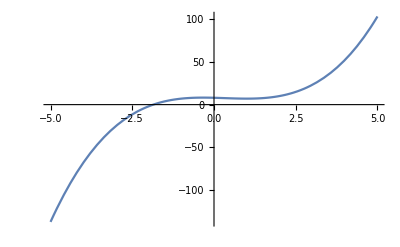

```mathematica
Plot[x^3-x^2-x+8,{x,-5,5}]
```

## 13.- Dada la función f(x)=10+3xe^(-0.2x). Estudiar la monotonía y los extremos relativos de f(x) en todo su dominio.

Solución:
La función f es una función continua (por ser composición de funciones continuas, polinomios y exponencial) y el dominio es todo R. 

Los candidatos a extremo relativo son los puntos donde se anula la primera derivada
f(x)=10+3 xe^(-0.2x)⇒f'(x)=e^(-0.2x)(3-0.6x)
f'(x)=0⟺e^(-0.2x)(3-0.6x)=0⟺3-0.6x=0⟺x=5

Existe un único candidato a extremo relativo, para estudiar si se trata de un máximo o un mínimo utilizamos el criteriode l segunda derivada
f(x)=10+3 xe^(-0.2x)⇒f'(x)=e^(-0.2x)(3-0.6x)⇒f''(x)=e^(-0.2x)(0.12x-1.2)
f''(5)=e^(-0.2*5)(0.12*5-1.2)<0
Por tanto en x=5 hay un máximo relativo

Para estudiar la monotonía aplicamos el criterio de la primera derivada
(-∞,5) ⟶f'(0)=e^(-0.2*0)(3-0.6*0)>0
(5,∞) ⟶f'(10)=e^(-0.2*10)(3-0.6*10)<0
La función es creciente en (-∞,5) y decreciente en (5,∞)

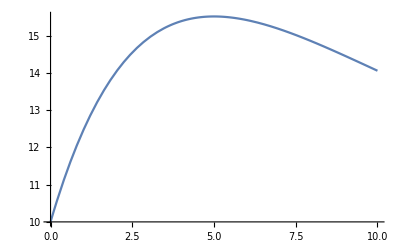

```mathematica
Plot[10+3x*Exp[-0.2x],{x,0,10}]
```

## 14.- Se quiere diseñar una lata con capacidad para 1 litro con forma de cilindro circular recto. Determinar las dimensiones que debe tener la lata, es decir, el radio de la base y la altura del cilindro que permita utilizar la menor cantidad posible de material.

Solución :
El desarrollo de una lata viene dado por:
-Graphics-
Sabemos que el volumen del cilindro es V_cilindro=A_base*h=πr^2*h y nos dicen que la capacidad de la lata es de 1L es decir, la condición que tenemos es que πhr^2=1 ⟹h=1/πr^2.
Se quiere utilizar la menor cantidad de material posible, esto es, se quiere minimizar el área del cilindro, busquemos la función que calcula el área del cilindro
A_cilindro=2*A_base+A_lateral=2 πr^2+2πrh=2πr(r+h)
Obtenemos así una función dependiente de dos parámetros, incluimos la condición (h=1/πr^2)para obtener una función de una variable
A_cilindro=2*A_base+A_lateral=2 πr^2+2πrh=2πr(r+h)⟹f(r)=2πr(r+1/πr^2)=2πr((πr^3+1)/πr^2)=2((πr^3+1)/r)

El ejercicio consiste en buscar el mínimo de la función f(r)=2((πr^3+1)/r).
Buscamos los puntos críticos, puntos donde se anula la derivada
f'(r)=2((3 πr^2*r-(πr^3+1))/r^2)=2((3 πr^3-πr^3-1)/r^2)=2((2 πr^3-1)/r^2)
f'(r)=0⟺2((2 πr^3-1)/r^2)=0⟺(2 πr^3-1)/r^2=0⟺2 πr^3-1=0⟺r=(1/(2π))^(1/3)=1/(2π)^(1/3)

El candidato a mínimo es r=1/(2π)^(1/3)aplicando el criterio de la segunda derivada comprobemos si se trata de un máximo o un mínimo
f''(r)=2((6 πr^2*r^2-2r*(2 πr^3-1))/r^4)=2((2 πr^4+2r)/r^4)=4((πr^3+1)/r^3)
f''(r)=4(((π(1/(2π)^(1/3)))^3-1)/((1/(2π)^(1/3))^3))=4((π/(2π)-1)/(1/(2π)))=12π>0
Por tanto, r=1/(2π)^(1/3) es un mínimo de la función. Así, las dimensiones de la lata de 1L de capacidad con menor superficie son r=1/(2π)^(1/3)y h=1/(π(1/(2π)^(1/3))^2)=(4/π)^(1/3)

Con Mathematica:

```mathematica
f[r_]:=2*Pi*r^2+2*Pi*r*(1/(Pi*r^2))
f[r]//Simplify
```

(2+2 π r^3)/r

```mathematica
Solve[f'[r]==0,r]
```

{{r→-(-1/(2 π))^(1/3)},{r→1/(2 π)^(1/3)},{r→(-1)^(2/3)/(2 π)^(1/3)}}

```mathematica
f''[1/(2 π)^(1/3)]
```

12 π

```mathematica
r=1/(2 π)^(1/3);
h=1/(Pi*r^2)
```

2^(2/3)/π^(1/3)

## 15.- (Julio 2023) Consideremos la figura formada por un rectángulo, de lados x (altura) y 2r (base), y un semicírculo de radio r. Si el perímetro de la figura resultante, L, está fijo, encontrar los valores de x y r para que el área sea máxima.

Solución:
El área de la figura es x*2r+(π  r^2)/2. El perímetro es 2x+2r+π*r =L. Despejando x=(L-2r-π*r)/2 y sustituyendo en el área   x*2r+(π  r^2)/2 = (L-2r-π*r)r+(π  r^2)/2=  L*r-2 r^2-(π  r^2)/2 =A(r).
Como x y r no pueden ser negativos, L-r(2+π)≥0, r≤L/(2+π). Por tanto debemos buscar el máximo de A(r)=L*r-2 r^2-(π  r^2)/2  en el intervalo [0,L/(2+π)]. 
Es una función polinómica de grado dos con coeficiente líder negativo, es continua y derivable en el intervalo. Tendrá por tanto máximo y mínimo absoluto. 
A’(r)=L-4r-π  r = 0 ⟹ r=L/(4+π)
Evaluamos A en los extremos del intervalo y donde se anula la derivada:
A(0)=L*0-2*0^2-(π*0^2)/2=0
A(L/(4+π))= L*L/(4+π)-2(L/(4+π))^2-(π (L/(4+π))^2)/2 =L^2/(4+π)-(2 L^2)/(4+π)^2-(π L^2)/(2(4+π)^2)=L^2/(2(4+π))(2-4/(4+π)-π/(4+π))=L^2/(2(4+π))
A(L/(2+π))=L*L/(2+π)-2(L/(2+π))^2-(π (L/(2+π))^2)/2=L^2/(2+π)-(2 L^2)/(2+π)^2-(π L^2)/(2(2+π)^2)=L^2/(2(2+π))(2-4/(2+π)-π/(2+π))=L^2/(2(2+π))((4+2π-4-π)/(2+π))=L^2/(2(2+π))(π/(2+π)) 

Comparamos  L^2/(2(4+π)) con L^2/(2(2+π))(π/(2+π)). Simplificando L^2/2 en las dos expresiones, tenemos 1/(4+π) y 1/(2+π)(π/(2+π)) . Multiplicando por (4+π) (2+π)^2, tenemos (2+π)^2= (4+4π+π^2) y π(4+π)=(4π+π^2). Por tanto, la primera expresión es la mayor. También, se puede razonar considerando que la función es un polinomio de grado dos y coeficiente líder negativo, lo que hace que en el punto donde se anula la derivada se tiene un máximo absoluto. 

El máximo se consigue en r=L/(4+π). El valor de x será x= (L-2r-π*r)/2 = (L-(2+π)*r)/2=(L-(2+π)*(L/(4+π)))/2=L/2(1-((2+π)/(4+π)))=L/2(2/(4+π))=L/(4+π)

## 16.- (Julio 2022) Calcular los máximos y mínimos absolutos de la función f(x) =|x^2-1| en [-1, 3].

Solución:
La función f es una función continua (por ser composición de funciones continuas, primero un polinomio y luego el valor absoluto) y el dominio es un intervalo cerrado y acotado. Por tanto, el teorema de Weierstrass asegura que existe máximo y mínimo absolutos.
Para encontrarlos debemos estudiar los extremos del intervalo, los puntos con derivada 0 del interior del intervalo, y los puntos donde no exista derivada de la función.
La función valor absoluto es derivable en todo punto, excepto en el 0. Veamos cuando x^2-1 es cero.
x^2-1 = 0 ⟹ x = ±1. Además, x^2-1 es mayor que cero cuando x es menor que -1 o mayor que 1. Por tanto
f(x)=Piecewise[{{x^2-1, si x <-1 ó x >1}, {1-x^2, si -1≤x ≤1}}]
La derivada es 2x o -2x, según el intervalo, y que solo se anularía en x=0 .
Por tanto debemos estudiar el valor de f en los extremos (x=-1, x=3), en los puntos con derivada cero (x=0) y los puntos del interior sin derivada (x=1).
Evaluando f(-1)=0, f(0)=1, f(1)=0, f(3)=8.
El valor máximo de f es 8 que se alcanza en el punto x=3, el valor mínimo de f es 0, que se alcanza en los puntos x=-1 y x=1.

Con Mathematica:

```mathematica
f[x_]:=Piecewise[{{x^2-1,x<-1},{1-x^2,-1<=x<=1},{x^2-1,x>1}}]
```

```mathematica
Solve[f'[x]==0,x]
```

{{x→0}}

```mathematica
f''[0]
```

-2

La función tiene un máximo relativo en x=0

```mathematica
{f[-1],f[0],f[1],f[3]}
```

{0,1,0,8}

La función tiene un máximo absoluto en x=3 que vale 8 y un mínimo absoluto en x=-1 y x=1 que vale 0

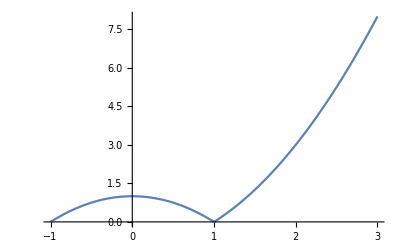

```mathematica
Plot[f[x],{x,-1,3}]
```

## 17.- (Enero 2022) Calcular los máximos y mínimos absolutos de la función f(x) =x^3-3 x^2+2 en el intervalo [1, 3].

Solución:
La función f(x) es una función continua por ser un polinomio (también es derivable por la misma razón). Al ser una función continua en un intervalo cerrado y acotado, el [1, 3], tiene máximo y mínimo absolutos.

Los máximos y mínimos absolutos se encuentran estudiando tres tipos de puntos:
a) Los extremos del intervalo. En este caso, x=1 y x=3.
b) Los puntos del interior del intervalo con derivada cero.
f’(x)= 3 x^2-6x
Calculamos cuándo 3 x^2-6x=0, y obtenemos 3 x^2-6x = 3x(x-2) =0. Será cierto cuando x=0 o x=2. El punto x=0, no está en el intervalo. Por tanto, solo consideramos x=2.
El único punto donde se anula la derivada en el intervalo es el punto x=2.
c) Los puntos donde no existe derivada. En este caso, la derivada existe en todos los puntos.

Basta ahora evaluar la función en los puntos que hemos encontrado:
f(1)= 1^3-3*1^2+2= 0, f(2)= 2^3-3*2^2+2= 8-12+2 = -2 , f(3)= 3^3-3*3^2+2= 27-27+2=2

El valor máximo de la función es 2, que se alcanza en el punto x=3. El valor mínimo de la función es -2 que se alcanza en el punto x=2.
Si dibujamos la gráfica con el Mathematica vemos lo que ocurre con la función.

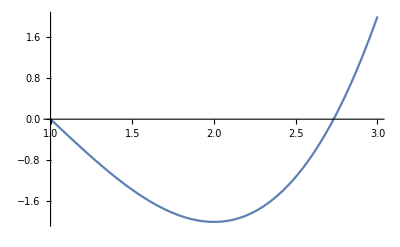

```mathematica
Plot[x^3-3 x^2+2,{x,1,3}]
```

Con Mathematica:

```mathematica
f[x_]:=x^3-3x^2+2
```

```mathematica
Solve[f'[x]==0,x]
```

{{x→0},{x→2}}

```mathematica
{f''[0],f''[2]}
```

{-6,6}

La función tiene un máximo relativo en x=0 y un mínimo relativo en x=2.

Para estudiar los extremos relativos no tenemos en cuenta el punto x=0 ya que no pertenece al intervalo [1,3]

```mathematica
{f[1],f[2],f[3]}
```

{0,-2,2}

La función tiene un máximo absoluto en x=3 que vale 2 y un mínimo absoluto en x=2 que vale -2

```mathematica
Plot[f[x],{x,1,3}]
```

-Graphics-

## 18.- (Enero 21) Calcular los máximos y mínimos absolutos de la función f(x) =|x^2-4| en el intervalo [-2,3].

Solución: 
La función f(x) es una función continua por ser composición de funciones continuas, la función polinómica x^2-4 y la función valor absoluto. Al ser una función continua en un intervalo cerrado y acotado, el [-2,3], tiene máximo y mínimo absolutos.
Los máximos y mínimos absolutos se encuentran estudiando tres tipos de puntos:
a) Los extremos del intervalo. En este caso x=-2 y x=3.
b) Los puntos del interior del intervalo con derivada cero.
f(x)=Piecewise[{{x^2-4,, cuando x^2-4≥ 0}, {-(x^2-4),, cuando x^2-4≤ 0}}] 
Calculamos cuándo x^2-4=0, y obtenemos x=±2. Si x>2 o x<-2, x^2-4>0. En cambio, si -2<x<2, x^2-4<0. Por tanto,
f(x)=Piecewise[{{x^2-4,, si 2≤ x ≤ 3}, {-(x^2-4),, si -2≤x≤2}}] ⟹ f ‘(x)=Piecewise[{{2x,, si 2< x ≤ 3}, {-2x,, si -2≤x<2}}]
El único punto donde se anula la derivada es el punto x=0.
c) Los puntos donde no existe derivada. En este caso, en el punto x=2, que es donde cambia la definición de la función, pasando del polinomio -2x al polinomio 2x.
Basta ahora evaluar la función en los puntos que hemos encontrado en cada uno de los tipos de puntos.
f(-2)=|(-2)^2-4|=0, f(0)=|0^2-4|=4, f(2)=|2^2-4|=0, f(3)=|3^2-4|=5.
El valor máximo de la función es 5, que se alcanza en el punto x=3. El valor mínimo de la función es 0 que se alcanza en dos puntos, el punto x=-2 y el punto x=2.

Con Mathematica:

```mathematica
f[x_]:=Piecewise[{{x^2-4,x<-2},{4-x^2,-2<=x<=2},{x^2-4,x>2}}]
```

```mathematica
Solve[f'[x]==0,x]
```

{{x→0}}

```mathematica
f''[0]
```

-2

La función tiene un máximo relativo en x=0

```mathematica
{f[-2],f[0],f[2],f[3]}
```

{0,4,0,5}

La función tiene un máximo absoluto en x=3 que vale 5 y un mínimo absoluto en x=-2 y x=2 que vale 0

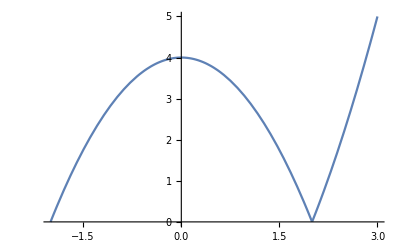

```mathematica
Plot[f[x],{x,-2,3}]
```

## 19.- (Enero 20) Calcular el máximo y mínimo absolutos de la función f(x)=x^4-2 x^2 con x en el intervalo [-1/2, 2].

Solución: 
Dado que es una función continua y derivable en un intervalo cerrado y acotado, tendrá máximo y mínimo absoluto, que alcanzará en los extremos del intervalo o en puntos con derivada cero (pues no hay puntos donde no exista la derivada).
f’(x)= 4x^3 - 4 x =4x(x^2-1). La derivada se anula en 0 y 1 (también se anularía en -1, pero este punto no está en el intervalo). Ahora, basta evaluar en los puntos de derivada 0 y en los extremos; f(-1/2)= -7/16, f(0)=0 , f(1)=-1 , f(2)=8. Por tanto el mínimo es -1, que se alcanza en el punto 1, y el máximo es 8, que se alcanza en el punto 2.

Con Mathematica:

```mathematica
f[x_]:=x^4-2x^2
```

```mathematica
Solve[f'[x]==0,x]
```

{{x→-1},{x→0},{x→1}}

```mathematica
{f''[-1],f''[0],f''[1]}
```

{8,-4,8}

La función tiene un máximo relativo en x=0 y dos mínimos relativos en x=-1 y x=1.

Estudiamos los máximos absolutos en el intervalo [-1/2,2]

```mathematica
{f[-1/2],f[0],f[1],f[2]}
```

{-7/16,0,-1,8}

La función tiene un máximo absoluto en x=2que vale 8 y un mínimo absoluto en x=1 que vale -1

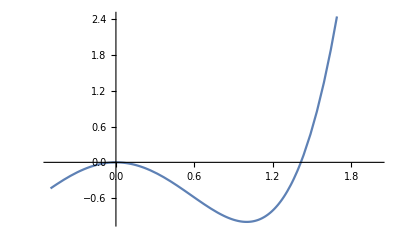

```mathematica
Plot[f[x],{x,-1/2,2}]
```

## 20.- (Enero 2019) Cuántas soluciones tiene la ecuación x^5+2x^3+3x+4=0.

Solución:
La función f(x)=x^5+2x^3+3x+4 es una función continua y derivable en toda la recta real.
En x=-1, f(-1)=-2, en x=0, f(0)=4.
Por el teorema de Bolzano, hay un valor entre -1 y 0 donde f se anula, por tanto hay una solución de la ecuación. 
Para ver si hay más, consideramos la derivada de la función, f ’(x)= 5 x^4+6x^2+3. Como f’(x) es siempre mayor que cero, la función es estrictamente creciente, por tanto no puede anularse en dos puntos y la ecuación tiene sólo una solución.

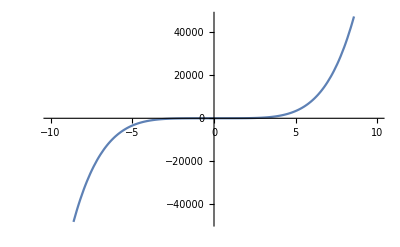

```mathematica
Plot[x^5+2x^3+3x+4,{x,-10,10}]
```

## 21.- (Enero 2018) Calcular el máximo y mínimo absolutos de la función f(x)=|4-x^2|con x en [-3,1].

Solución:
La función f(x) es continua (por ser diferencia y composición de funciones continuas) y en el intervalo [-3,1] (cerrado y acotado) tiene máximo y mínimo absolutos (Teorema de Weierstrass). Para calcular el máximo y el mínimo absolutos calculamos los puntos que son candidatos: extremos del intervalo, puntos donde se anula la derivada, puntos donde la función no sea derivable.

f(x)=|4-x^2|=Piecewise[{{x^2-4,, cuando 4-x^2≤0⟺4 ⩽x^2⟺x≤-2 ó 2⩽x (en este caso,-3≤x≤-2)}, {4-x^2,, cuando4-x^2≥0⟺4 ≥x^2⟺-2≤x≤2 (en este caso,-2≤x≤1)}}] 

La derivada f ’(x)=
f ’(x)=Piecewise[{{2x,, cuando -3≤x<-2)}, {-2x,, cuando-2<x≤1)}}]

En el punto -2, la función no es derivable.

	1) Extremos: -3, 1.
	2) Puntos con derivada cero: 0.
	3) Puntos donde f no es derivable: -2.

Ahora evaluamos f en esos puntos
f(-3)= |4-(-3)^2|=5, f(1)=|4-1^2|=3, f(0)=|4-0^2|=4, f(-2)=|4-(-2)^2|=0.
Por tanto, el máximo está en el punto -3, donde la función vale 5 y el mínimo está en el punto -2, donde la función vale 0.

Con Mathematica:

```mathematica
f[x_]:=Piecewise[{{x^2-4,x<-2},{4-x^2,-2<=x<=2},{x^2-4,x>2}}]
```

```mathematica
f[x]
```

Piecewise[{{-4+x^2, x<-2}, {4-x^2, -2≤x≤2}, {-4+x^2, x>2}, {0, True}}]

```mathematica
Solve[f'[x]==0,x]
```

{{x→0}}

```mathematica
f''[0]
```

-2

La función tiene un máximo relativo en x=0

```mathematica
{f[-3],f[-2],f[0],f[1]}
```

{5,0,4,3}

La función tiene un máximo absoluto en x=-3 que vale 5 y un mínimo absoluto en x=-2 que vale 0

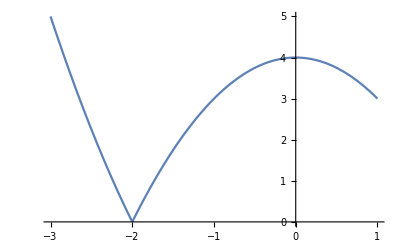

```mathematica
Plot[f[x],{x,-3,1}]
```

## 22.- (Enero 2018) Para aproximar las soluciones real de la ecuación x^3+x+1=0, considerar la función f(x) = x^3+x+1. ¿Es continua? ¿Es derivable? Evaluarla en -1 y 1. ¿Cuantas raíces tiene la ecuación? Aplicar el método de bisección 3 veces partiendo del intervalo [-1,1].

Solución:
La función f es continua en toda la recta real pues es un polinomio. También es derivable, pues es un polinomio. 
	f(-1)=-1-1+1=-1
	f(1)=1+1+1=3
Como el signo de la función f en -1 y en 1 son opuestos (siendo f continua; Teorema de Bolzano), la función se anula en algún punto entre -1 y 1. Por tanto, la ecuación tiene al menos una raíz. Para saber si tiene más, estudiamos la derivada de la función.
	f ’(x) = 3 x^2+1 
Vemos que la derivada de la función es siempre mayor que cero, la función es siempre estrictamente creciente y no puede tener más de un cero. Por tanto, hay una única solución de la ecuación y está entre -1 y 1.

Aplicamos ahora el método de bisección. Partimos del intervalo [-1,1] donde la función, que es continua, presenta cambio de signo y tiene por tanto una raíz.
	a_0= -1, b_0= 1, m_0= (a_0+b_0)/2= 0, f(a_0)=-1, f(b_0)=3, f(m_0)=1
Como en el punto medio la función tiene el mismo signo que en el extremo de la derecha reducimos el intervalo por esa parte
	a_1= -1, b_1= 0, m_1= (a_1+b_1)/2= -1/2, f(a_1)=-1, f(b_1)=1, f(m_1)=(-1/2)^3+(-1/2)+1=(-1/8)-(1/2)+1>0

Como en el punto medio la función tiene el mismo signo que en el extremo de la derecha reducimos el intervalo por esa parte
	a_2= -1, b_2= -1/2, m_2= (a_2+b_2)/2= -3/4, f(a_2)=-1, f(b_2)>0, f(m_2)=(-3/4)^3+(-3/4)+1=(-27/64)-(3/4)+1= (-27/64)-(48/64)+1=(-75/64)+1<0.
Como en el punto medio la función tiene el mismo signo que en el extremo de la izquierda, reducimos el intervalo por esa parte.
Tras tres pasos por el método de bisección hemos llegado a que la solución de la ecuación está en el intervalo [-3/4,-1/2].

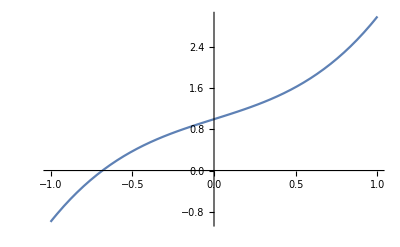

```mathematica
Plot[x^3+x+1,{x,-1,1}]
```